Sketches BAC Band Structure

```mathematica
vx=0.2;
ed=0.2;
Ep=(k^2+ed+√((k^2-ed)^2+4 vx^2))/2;
Em=(k^2+ed-√((k^2-ed)^2+4 vx^2))/2;
```

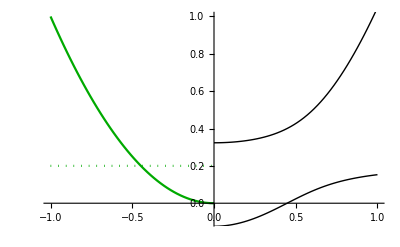

```mathematica
Show[Plot[{k^2,ed},{k,-1,0},PlotStyle->{Darker[Green],{Darker[Green],Dotted}}],
Plot[{Ep,Em},{k,0,1},PlotStyle->{{Black,Thick}}],PlotRange->{{-1,1},{-0.1,1}}]
```

Calculates ω_p

```mathematica
(*Subscript[ω, p0] as a function of μ*)
wp0[vx_,ed_,u_]:=√(8/(3*137*π))(vx^2/(ed-u)+u)^(3/4)(ed-u)^3/(((ed-u)^2+vx^2)^(3/2));
```

```mathematica
(*Subscript[E, x] as a function μ, considering both Subscript[E, d] positive and negative*)
Exx[vx_,ed_,u_]:=If[u>ed-vx,2vx,√((vx^2/(ed-u)-ed+u)^2+4 vx^2)];
Ex[vx_,ed_,u_]:=If[ed>0,Exx[vx,ed,u],√(ed^2+4 vx^2)];
```

```mathematica
(*Subscript[ϵ, x](ω) integral, memoized*)
Epsx[vx_,ed_,u_,l_,w_]:=Epsx[vx,ed,u,l,w]=1+(8 vx^2 l^2)/(137π)NIntegrate[k^2/(√((k^2-ed)^2+4 vx^2)((k^2-ed)^2+4 vx^2-w^2)),{k,0,√(vx^2/(ed-u)+u)}];
```

```mathematica
(*solves for Subscript[ω, p] by halving, memoized*)
wp[vx_,ed_,u_,l_]:=wp[vx,ed,u,l]=
Module[{wr=(1-10^-5)Ex[vx,ed,u],wl=0},
While[wr-wl>2*10^-3 Ex[vx,ed,u],
wm=(wr+wl)/2;
If[wm^2 Epsx[vx,ed,u,l,wm]>wp0[vx,ed,u]^2,
wr=wm,wl=wm];
];
wm
]
```

Sketches the Window

```mathematica
Ed=10^-8/(√2);Vx=10^-8;l=500;
```

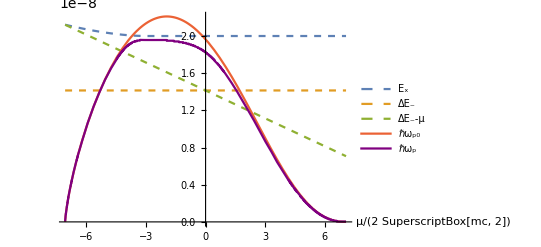

```mathematica
Plot[{Ex[Vx,Ed,u],(Ed+√(Ed^2+4 Vx^2))/2,(Ed+√(Ed^2+4 Vx^2))/2-u,wp0[Vx,Ed,u],wp[Vx,Ed,u,l]},{u,(Ed-√(Ed^2+4 Vx^2))/2,Ed},PlotStyle->{Dashed,Dashed,Dashed,Thick,{Thick,Purple}},PlotLegends->{"E_x","ΔE_-","ΔE_--μ","ℏω_p0","ℏω_p"},AxesLabel->{"μ/(2 SuperscriptBox[mc, 2])"}]
```